# QM Dynamics

### Connectivity Matrix (Hopping) H

```mathematica
H = {{0, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0}, {0, 1, 0, 1, 0, 0},{0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 0}};
H2 = {{0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 0},{0, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0}, {0, 1, 0, 1, 0, 0}};
MatrixForm[H]
```

(0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0)

### Transfer matrix of Markov process

```mathematica
Clear[x];
T = (1 - 2 x^2) * IdentityMatrix[6] + x^2 * H
MatrixForm[T]
```

{{1-2 x^2,x^2,0,0,0,x^2},{x^2,1-2 x^2,x^2,0,0,0},{0,x^2,1-2 x^2,x^2,0,0},{0,0,x^2,1-2 x^2,x^2,0},{0,0,0,x^2,1-2 x^2,x^2},{x^2,0,0,0,x^2,1-2 x^2}}

(1-2 x^2 | x^2 | 0 | 0 | 0 | x^2
x^2 | 1-2 x^2 | x^2 | 0 | 0 | 0
0 | x^2 | 1-2 x^2 | x^2 | 0 | 0
0 | 0 | x^2 | 1-2 x^2 | x^2 | 0
0 | 0 | 0 | x^2 | 1-2 x^2 | x^2
x^2 | 0 | 0 | 0 | x^2 | 1-2 x^2)

### Time step

```mathematica
x = 0.1;
MatrixForm[T]
```

(0.98 | 0.01 | 0 | 0 | 0 | 0.01
0.01 | 0.98 | 0.01 | 0 | 0 | 0
0 | 0.01 | 0.98 | 0.01 | 0 | 0
0 | 0 | 0.01 | 0.98 | 0.01 | 0
0 | 0 | 0 | 0.01 | 0.98 | 0.01
0.01 | 0 | 0 | 0 | 0.01 | 0.98)

### Markov process starting with particle on site #1

```mathematica
Markov[n_, m_] := Module[
{x = {1, 0, 0, 0, 0, 0},u = {0}},
For[i = 0, i < n, i++, x = T.x;
y = x[[m]];
AppendTo[u, y]];
u];
```

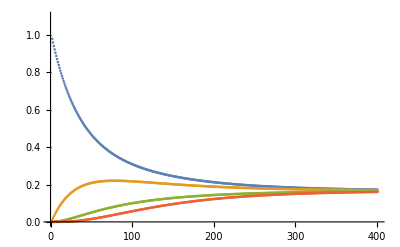

```mathematica
ListPlot[{Markov[400, 1], Markov[400, 2], Markov[400, 3], Markov[400, 4]},PlotRange -> {0,1.1}]
```

### Unitary matrix of QM time evolution U=exp(itH) from particle localized on site #1

```mathematica
U=Round[N[MatrixExp[ⅈ x H]],0.0001];
MatrixForm[U]//N
```

(0.99 | 0.+0.0995 ⅈ | -0.005 | 0.-0.0003 ⅈ | -0.005 | 0.+0.0995 ⅈ
0.+0.0995 ⅈ | 0.99 | 0.+0.0995 ⅈ | -0.005 | 0.-0.0003 ⅈ | -0.005
-0.005 | 0.+0.0995 ⅈ | 0.99 | 0.+0.0995 ⅈ | -0.005 | 0.-0.0003 ⅈ
0.-0.0003 ⅈ | -0.005 | 0.+0.0995 ⅈ | 0.99 | 0.+0.0995 ⅈ | -0.005
-0.005 | 0.-0.0003 ⅈ | -0.005 | 0.+0.0995 ⅈ | 0.99 | 0.+0.0995 ⅈ
0.+0.0995 ⅈ | -0.005 | 0.-0.0003 ⅈ | -0.005 | 0.+0.0995 ⅈ | 0.99)

### QM time evolution + measurement x(n)=U^n x(0), y = | x_m(n) |^2

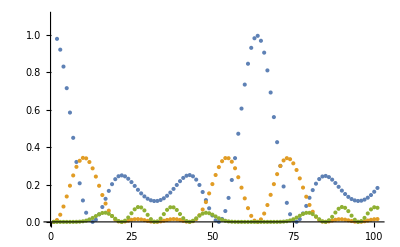

```mathematica
Quant[n_, m_] := Module[
{x = {1, 0, 0, 0, 0, 0}, u = {0}}, 
For[i = 0, i < n, i++, x = U.x;
y = Abs[x[[m]]]^2;
AppendTo[u, y]];
u];
ListPlot[{Quant[100, 1], Quant[100, 2], Quant[100, 3] Quant[100, 4]},
PlotRange ->{0, 1.1}]
```

### Eigenvalues and eigenvectors of the Hamiltonian H

```mathematica
eig = Eigensystem[N[H]];
ee = eig[[1]]
```

{2.,-2.,1.,1.,-1.,-1.}

### Time evolution as above obtained using eigenstates x_m(n)=sum_i <m| i><i|1> exp(i t E_i)

normalize eigenvectors

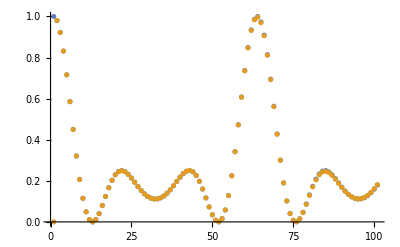

```mathematica
evec = Module[
{x = eig[[2]]}, 
For[i = 1, i < 7, i++,
y = Sqrt[x[[i]].x[[i]]];
x[[i]] = x[[i]] / y];
x];
Quant2[n_, m_] := Sum[evec[[i]][[1]] * evec[[i]][[m]] * Exp[-ⅈ * n * x * ee[[i]]], {i, 1, 6}];
ListPlot[{Table[Abs[Quant2[n, 1]]^2, {n, 0, 100}],Quant[100,1]}]
```

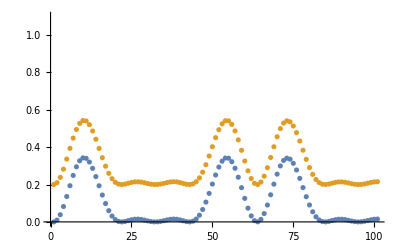

```mathematica
ListPlot[{ Quant[100, 2],Quant[100, 6]+0.2},
PlotRange ->{0, 1.1}]
```

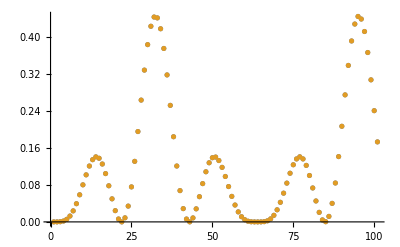

```mathematica
ListPlot[{Table[Abs[Quant2[n, 3]]^2, {n, 0, 100}], Table[Abs[Quant2[n, 5]]^2, {n, 0, 100}]}]
```

```mathematica
Table[Abs[Quant2[n, 2]]^2,{n, 0, 20}]//N
```

{0.,0.00990043,0.0384275,0.0822089,0.136106,0.193863,0.248895,0.295091,0.327539,0.343074,0.340577,0.320999,0.287118,0.243069,0.193728,0.144049,0.0984285,0.0602087,0.0313676,0.012428,0.00258386}

```mathematica
MatrixForm[evec]
```

(-0.408248 | -0.408248 | -0.408248 | -0.408248 | -0.408248 | -0.408248
-0.408248 | 0.408248 | -0.408248 | 0.408248 | -0.408248 | 0.408248
0.288675 | -0.288675 | -0.57735 | -0.288675 | 0.288675 | 0.57735
0.5 | 0.5 | -1.11022×10^-16 | -0.5 | -0.5 | 0.
-0.288675 | -0.288675 | 0.57735 | -0.288675 | -0.288675 | 0.57735
0.5 | -0.5 | -1.11022×10^-16 | 0.5 | -0.5 | 0.)

```mathematica
MatrixForm[H]
```

(0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0)